```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bcl206/Documents/GitHub/hmm_movement/src

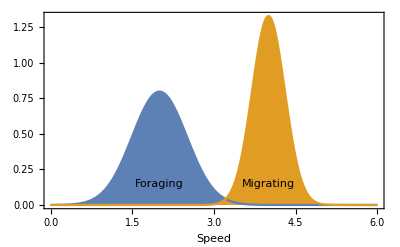

```mathematica
g=Show[Plot[{PDF[NormalDistribution[2, 0.5],x],PDF[NormalDistribution[4, 0.3],x]},{x,0,6},FillingStyle->Axis,Filling->Axis,Frame->{True,False,False,False},Axes->False,FrameTicks->None,FrameLabel->{"Speed"},LabelStyle->{Black,FontSize->16},Epilog->{Style[Text["Foraging", {2,0.15}],FontSize->16,White],Style[Text["Migrating", {4,0.15}],FontSize->16,White]}]]
```

```mathematica
Export["foraging_migrating.pdf",g]
```

foraging_migrating.pdf

```mathematica
Subscript[t,1]
```

t_1

```mathematica
ticks={{1,"t_1"},{2,"t_2"},{3,"t_3"}, {4,"t_4"}};
```

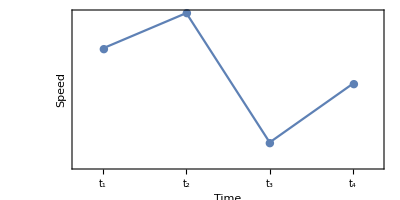

```mathematica
g2=ListLinePlot[{1, 1.3, 0.2, 0.7},Frame->{True,True,False,False},Axes->None,PlotRange->{{0.7,4.3},Full},PlotMarkers->{"●"},FrameLabel->{"Time", "Speed"},FrameTicks->{ticks,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2]
```

```mathematica
Export["hmm_time_series.pdf",g2]
```

hmm_time_series.pdf

## Longer series

```mathematica
p=HiddenMarkovProcess[{0.5,0.5},{{0.7,0.3},{0.25,0.75}},{NormalDistribution[2,0.5],NormalDistribution[4,0.3]}];
data=RandomFunction[p,{0,20}];
data1=(data//Normal)[[1]];
states=(FindHiddenMarkovStates[data,p]//Normal)[[1,All,2]];
state2=Flatten@Position[states, 2];
state1=Flatten@Position[states,1];
```

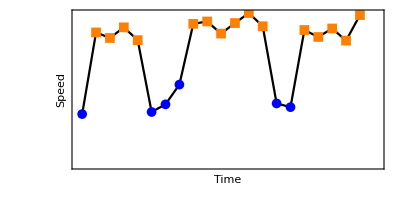

```mathematica
g2=Show[ListLinePlot[data,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,21.3},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic, Medium}]]
```

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x]^0.5, {x,-∞,∞}]
```

$Aborted

## Multiple modes of movement: infinite HMMs

```mathematica
n=400;
p=HiddenMarkovProcess[{1,0,0},{{0.7,0.3,0.00},{0.295,0.7,0.005},{0.00,0.005,0.995}},{NormalDistribution[1,0.5],NormalDistribution[5,0.3],NormalDistribution[10,0.3]}];
data=RandomFunction[p,{0,n}];
data1=(data//Normal)[[1]];
states=(FindHiddenMarkovStates[data,p]//Normal)[[1,All,2]];
state2=Flatten@Position[states, 2];
state1=Flatten@Position[states,1];
state3=Flatten@Position[states, 3];
```

```mathematica
states
```

{1,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,2,2,2,2,2,2,2,1,1,2,2,2,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,2,2,2,2,1,2,1,2,2,2,1,2,2,2,2,2,2,2,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,1,1,1,1,1,1,2,2,1,2,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,2,2,1,2,1,1,2,2,2,2,1,2,2,2,2,2,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,1,1,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,1,2,2,2,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,1,1,1,1,1,1,1,1,2,2,2,2,2,1,1,1,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,1,1,1,1,1,2,2,2,1,1,1,2,1,1,1,1,1,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
data1
```

{{0,0.699626},{1,0.931244},{2,0.776451},{3,1.75701},{4,5.43237},{5,5.1585},{6,4.34968},{7,4.84942},{8,5.04676},{9,4.78891},{10,4.86574},{11,5.78679},{12,5.15206},{13,1.31427},{14,0.9733},{15,1.32535},{16,1.43452},{17,4.72691},{18,4.568},{19,5.18452},{20,4.74089},{21,4.79154},{22,5.21742},{23,5.11998},{24,5.38585},{25,5.06987},{26,5.52193},{27,1.43873},{28,0.855676},{29,4.9873},{30,5.0625},{31,4.98998},{32,1.08092},{33,0.875096},{34,1.14074},{35,5.1855},{36,5.10123},{37,4.72902},{38,1.07618},{39,1.20478},{40,1.56619},{41,1.51879},{42,0.966273},{43,0.584799},{44,1.95228},{45,0.283156},{46,1.83524},{47,5.12943},{48,1.08876},{49,0.41103},{50,0.824904},{51,1.0568},{52,5.2695},{53,4.61327},{54,5.7153},{55,4.85588},{56,4.30735},{57,1.05559},{58,5.0913},{59,0.969186},{60,5.0084},{61,5.03458},{62,4.94482},{63,1.11199},{64,4.85247},{65,5.3579},{66,4.62971},{67,5.18988},{68,5.02936},{69,4.54007},{70,4.83879},{71,0.330781},{72,1.00685},{73,0.974185},{74,1.56882},{75,1.53803},{76,1.03151},{77,5.26278},{78,4.88829},{79,4.68582},{80,5.38754},{81,5.08881},{82,5.14588},{83,4.67609},{84,4.8593},{85,5.53217},{86,5.09452},{87,4.97004},{88,5.30927},{89,1.75357},{90,1.43627},{91,5.01866},{92,1.01035},{93,0.764375},{94,0.811078},{95,1.62091},{96,4.79286},{97,2.29065},{98,1.41359},{99,1.85329},{100,0.257673},{101,0.644052},{102,0.468029},{103,5.07769},{104,4.90487},{105,4.99385},{106,4.97002},{107,4.71454},{108,5.07551},{109,5.11185},{110,4.52399},{111,1.37162},{112,4.43765},{113,4.84839},{114,4.80891},{115,4.66185},{116,1.80771},{117,0.901411},{118,1.07965},{119,1.88916},{120,-0.118511},{121,1.1465},{122,1.33258},{123,4.67153},{124,4.89213},{125,1.52495},{126,4.80107},{127,5.01435},{128,5.26716},{129,0.669981},{130,0.246616},{131,0.748622},{132,1.45689},{133,4.95294},{134,0.634612},{135,-0.175048},{136,0.658582},{137,0.632528},{138,0.117428},{139,0.161718},{140,0.958877},{141,-0.245748},{142,0.491549},{143,0.522618},{144,1.13517},{145,5.22448},{146,4.71694},{147,4.72669},{148,4.88446},{149,1.51062},{150,5.07363},{151,5.03092},{152,0.871625},{153,4.62003},{154,0.504046},{155,0.0725713},{156,5.48644},{157,4.91167},{158,5.22762},{159,5.2841},{160,0.382978},{161,4.7133},{162,4.85449},{163,4.89277},{164,5.64606},{165,4.40624},{166,1.27037},{167,0.648879},{168,1.59687},{169,0.569196},{170,1.27978},{171,1.136},{172,1.25628},{173,1.16793},{174,5.2154},{175,5.09578},{176,5.02835},{177,4.75937},{178,4.82385},{179,4.74136},{180,4.64989},{181,4.79134},{182,4.94331},{183,1.39747},{184,1.3078},{185,5.08676},{186,5.38943},{187,5.17501},{188,0.652992},{189,5.0774},{190,4.9663},{191,5.6042},{192,5.07747},{193,4.84521},{194,4.69544},{195,4.96774},{196,4.77067},{197,0.852394},{198,5.20013},{199,5.26335},{200,5.10123},{201,4.77153},{202,0.685932},{203,0.628922},{204,4.88272},{205,4.55439},{206,5.58652},{207,4.91464},{208,5.52774},{209,5.41995},{210,1.38673},{211,0.667449},{212,0.890496},{213,4.93927},{214,4.41073},{215,4.43933},{216,5.00891},{217,5.09792},{218,5.1025},{219,4.82367},{220,5.03135},{221,4.65611},{222,5.14008},{223,0.905593},{224,4.36328},{225,5.16488},{226,1.12545},{227,5.08573},{228,5.06456},{229,1.71249},{230,0.891523},{231,0.00226537},{232,0.60957},{233,0.936137},{234,1.12681},{235,0.666909},{236,1.14284},{237,4.79596},{238,4.97746},{239,5.02938},{240,5.49507},{241,5.18095},{242,0.549191},{243,0.541973},{244,0.934426},{245,1.08031},{246,4.37839},{247,4.81706},{248,5.00178},{249,4.7011},{250,0.381439},{251,5.01868},{252,4.68488},{253,5.00398},{254,4.97167},{255,4.93929},{256,4.68564},{257,4.7739},{258,5.45126},{259,4.48181},{260,5.26839},{261,1.25137},{262,4.38984},{263,5.13338},{264,1.17028},{265,5.13277},{266,5.53604},{267,4.66914},{268,4.76713},{269,0.241007},{270,0.838354},{271,1.31989},{272,0.528439},{273,0.78552},{274,5.20547},{275,4.8479},{276,4.99979},{277,0.779868},{278,0.284268},{279,1.20147},{280,5.35069},{281,2.29633},{282,1.22682},{283,0.680103},{284,0.30835},{285,1.00667},{286,5.20651},{287,5.23041},{288,10.5902},{289,9.97657},{290,10.2887},{291,9.42744},{292,10.0325},{293,9.67717},{294,9.95764},{295,10.07},{296,10.7751},{297,9.79155},{298,9.66601},{299,9.34551},{300,9.97023},{301,9.80112},{302,9.61645},{303,10.0924},{304,10.1847},{305,9.6709},{306,10.4504},{307,10.1333},{308,10.3451},{309,10.2366},{310,10.4171},{311,10.8962},{312,10.7241},{313,10.1665},{314,10.4176},{315,9.8759},{316,9.9735},{317,10.3678},{318,9.90989},{319,10.0022},{320,9.64628},{321,10.3064},{322,9.84386},{323,10.624},{324,10.228},{325,10.1701},{326,9.60478},{327,9.57543},{328,10.3349},{329,10.3988},{330,10.1453},{331,10.1857},{332,10.1947},{333,10.0245},{334,9.93199},{335,9.58842},{336,10.1749},{337,10.0667},{338,9.9142},{339,10.3447},{340,9.92276},{341,10.4372},{342,10.4486},{343,9.80622},{344,10.0206},{345,10.3773},{346,10.4605},{347,10.2288},{348,10.0561},{349,9.64491},{350,9.92681},{351,10.3894},{352,9.72163},{353,10.1035},{354,9.51303},{355,9.87361},{356,10.1899},{357,9.86279},{358,10.1179},{359,10.215},{360,10.1332},{361,9.72589},{362,9.8978},{363,10.4145},{364,10.6675},{365,10.3327},{366,9.74274},{367,10.2673},{368,10.0248},{369,10.2519},{370,10.6164},{371,9.90415},{372,10.2494},{373,9.91772},{374,9.8478},{375,10.0819},{376,10.2787},{377,9.47862},{378,10.2082},{379,9.52738},{380,10.0049},{381,9.74309},{382,9.9812},{383,10.4534},{384,10.2362},{385,10.1071},{386,9.85065},{387,9.77536},{388,9.94583},{389,10.1638},{390,9.87094},{391,10.4424},{392,9.60708},{393,10.1288},{394,10.3489},{395,10.5419},{396,10.1748},{397,9.69104},{398,9.91058},{399,9.81774},{400,10.0747}}

```mathematica
Manipulate[Show[ListLinePlot[data1,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,a},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]],data1[[state3]]},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Medium}]],{a,20,n}]
```

```mathematica
g=Table[Show[ListLinePlot[data,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,a},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]],data1[[state3]]},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Medium}]],{a,20,n,2}];
```

$Aborted

```mathematica
Table[Export[StringJoin["../figures/cartoon/ihmm_",ToString@i, ".png"],g[[i]],ImageResolution->500],{i,1,Length@g,1}];
```

```mathematica
Export["../data/hmm_test.csv",data1]
```

../data/hmm_test.csv

## Mixture models

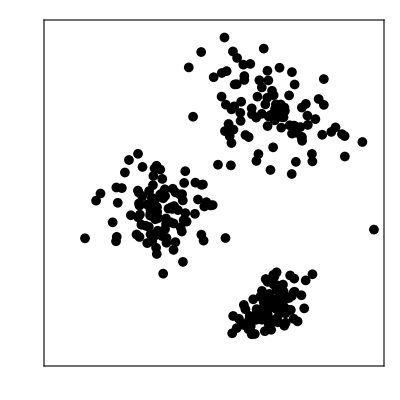

```mathematica
n=100;
μ1={0,0};
Σ1={{0.5,0},{0,0.5}};
μ2={3,3};
Σ2={{1,-0.5},{-0.5,1}};
μ3={3,-3};
Σ3={{0.2,0.1},{0.1,0.2}};
x1=RandomVariate[MultinormalDistribution[μ1,Σ1],n];
x2=RandomVariate[MultinormalDistribution[μ2,Σ2],n];
x3=RandomVariate[MultinormalDistribution[μ3,Σ3],n];
xmin=-3;
xmax=6;
ymin=-4.5;
ymax=5.5;
ppoints=50;
g1=Show[ContourPlot[PDF[MultinormalDistribution[μ1,Σ1],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.05]],ContourStyle->Blue,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ContourPlot[PDF[MultinormalDistribution[μ2,Σ2],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.05]],ContourStyle->Orange,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ContourPlot[PDF[MultinormalDistribution[μ3,Σ3],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.1]],ContourStyle->Purple,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None]];
g2=Show[g1,ListPlot[{x1,x2,x3},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Small}]];
g3=Show[ContourPlot[PDF[MultinormalDistribution[μ3,Σ3],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.1]],ContourStyle->White,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ListPlot[{x1,x2,x3},PlotStyle->Black,PlotMarkers->{"●", Small}]]
```

```mathematica
Export["../figures/mixture_models_1.pdf",g1]
Export["../figures/mixture_models_2.pdf",g2]
Export["../figures/mixture_models_3.pdf",g3]
```

../figures/mixture_models_1.pdf

../figures/mixture_models_2.pdf

../figures/mixture_models_3.pdf